# Integración

## Variables consideradas

### People = 500 Time = {0, 500, 1000, 1500, 2000, 2500, 3000, 3500, 4000, 4500, 5000} Capacity = 5

```mathematica
time={0,500,1000,1500,2000,2500,3000,3500,4000,4500,5000};
```

## Carga de redes

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
redes=Table[Import[StringJoin["Redes/Integracion/network-500-5-",IntegerString[i],".g6"]],{i,0,5000,500}];
```

```mathematica
randomizeGraph[g_]:=Module[{randGraph},
randGraph=RandomGraph[{VertexCount[g],EdgeCount[g]}];
Return[randGraph];
];
```

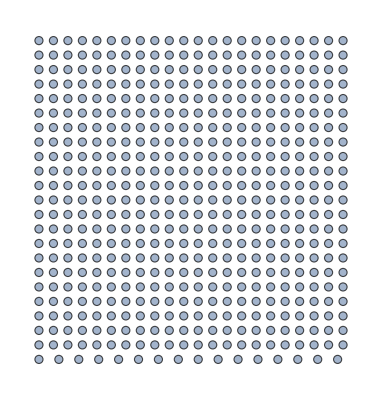
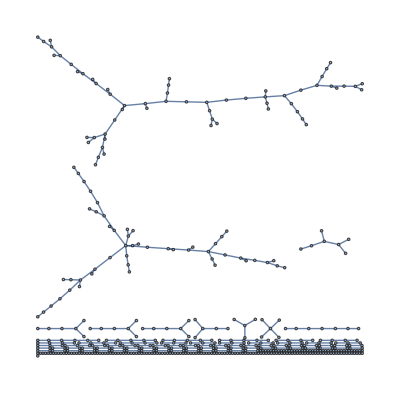
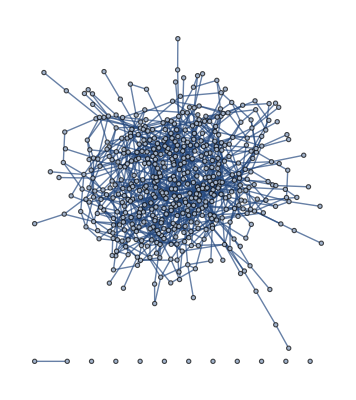
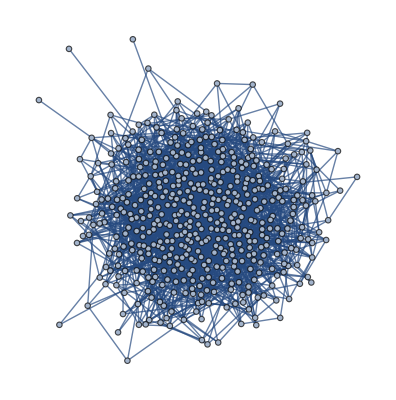
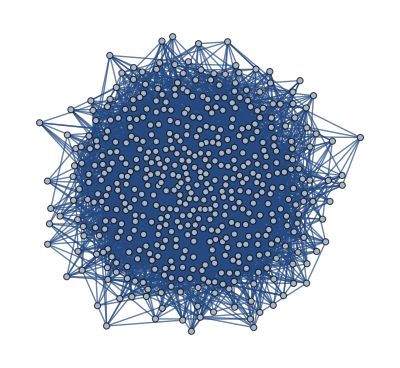
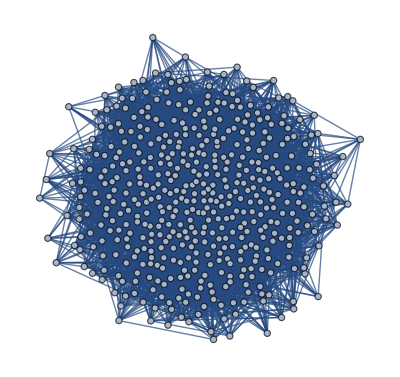
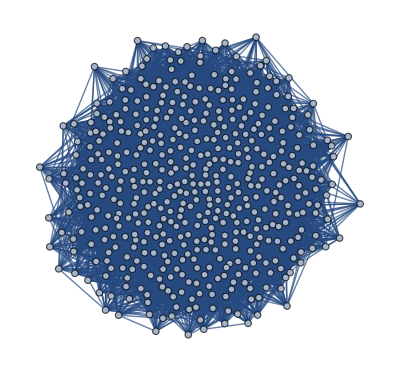
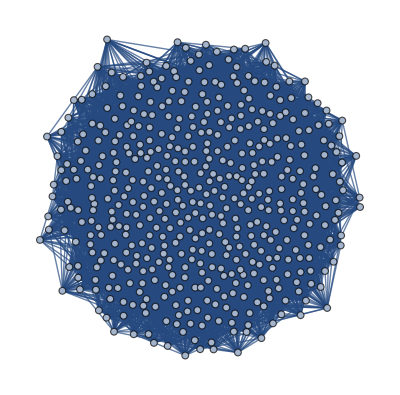

```mathematica
aleatorias=Map[randomizeGraph,redes]
```

```mathematica
evolucionModelo=Table[Length[ConnectedComponents[redes[[i]]]],{i,1,11,1}]
```

{500,301,119,39,15,6,2,1,3,1,1}

```mathematica
evolucionAleatorias=Table[Length[ConnectedComponents[aleatorias[[i]]]],{i,1,11,1}]
```

{500,250,12,1,1,1,1,1,1,1,1}

```mathematica
datosPlot1=Table[{time[[t]],evolucionModelo[[t]]},{t,1,Length[time],1}];
```

```mathematica
datosPlot2=Table[{time[[t]],evolucionAleatorias[[t]]},{t,1,Length[time],1}];
```

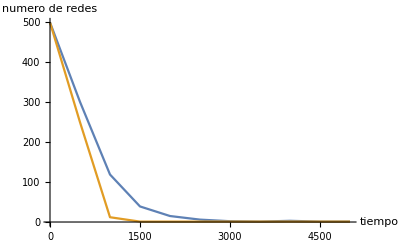

```mathematica
ListLinePlot[{datosPlot1,datosPlot2},AxesLabel->{"tiempo","numero de redes"}]
```

```mathematica
Map[Length,FindClique[redes[[11]],Infinity,All]]
```

```mathematica
allCliquesModelo=Table[Map[Length,FindClique[redes[[i]],Infinity,All]],{i,2,Length[time],1}];
```

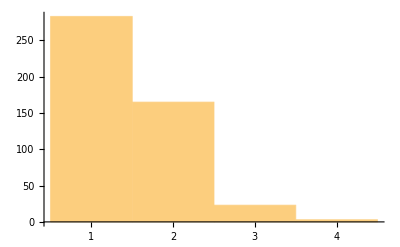
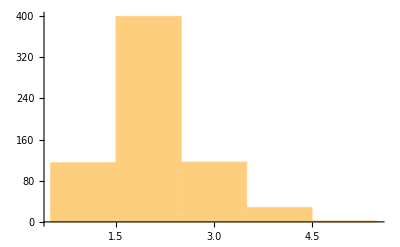
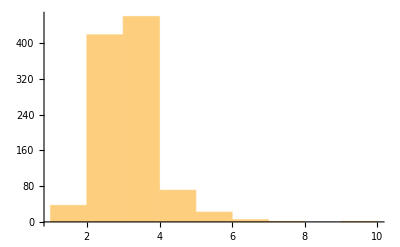
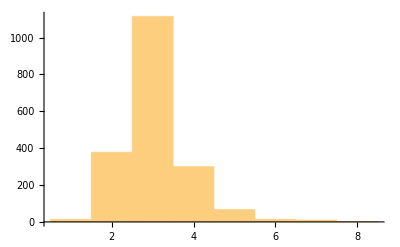
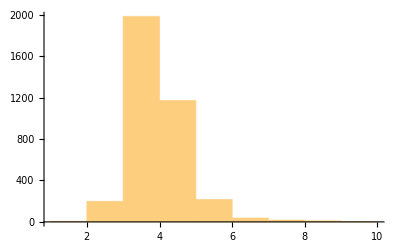
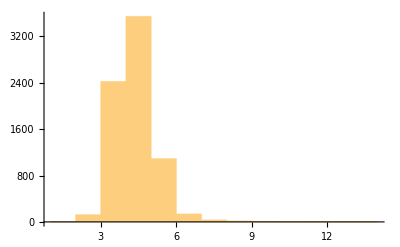
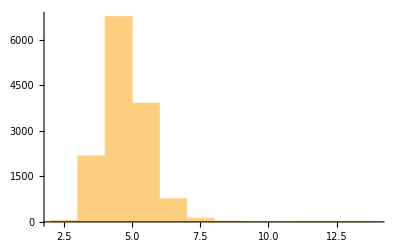
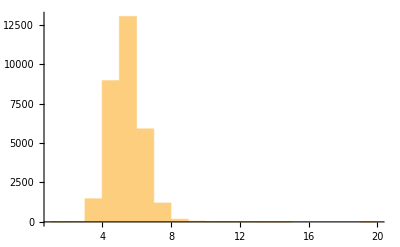

```mathematica
Map[Histogram,allCliquesModelo]
```

```mathematica
allCliquesAleatorias=Table[Map[Length,FindClique[aleatorias[[i]],Infinity,All]],{i,2,Length[time],1}];
```

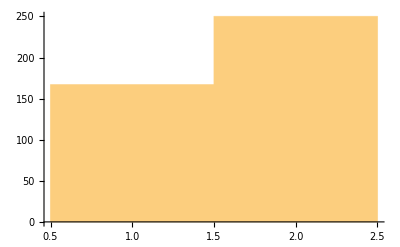
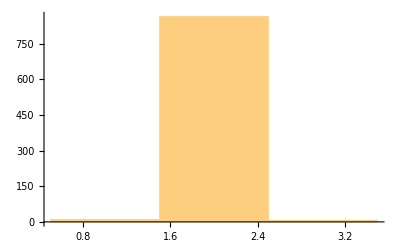
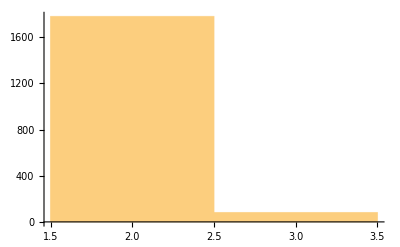
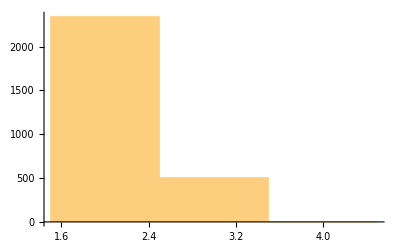
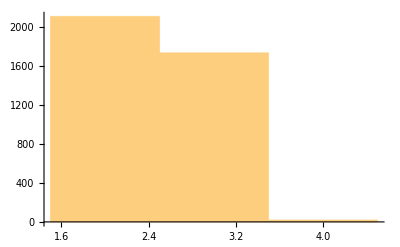
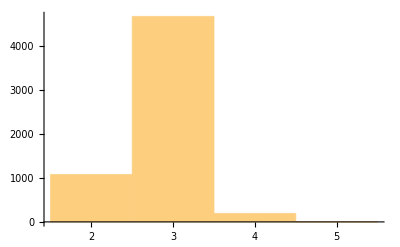
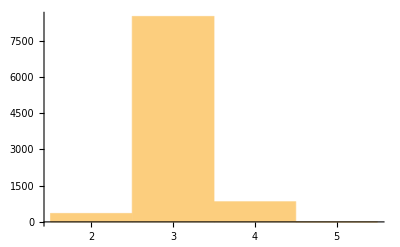
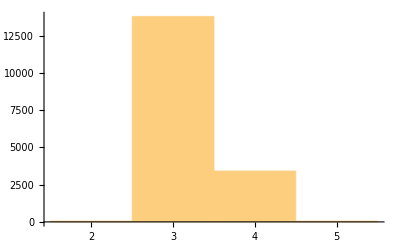

```mathematica
Map[Histogram,allCliquesAleatorias]
```